#### RUN FIRST: Import data and sort by date (each row of data is a day)

```mathematica
import
```

{{0,2154440895,6.7.139.3624,2016-04-11 02:51:15.896000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Kisada', 'Skoobz007', 'Hans Trolo', 'Croatian Rambo', 'lHaveTwoDads', 'Vapulate', 'Stride Max', 'GigglePuss', 'BlackTea8', 'woochi12345'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Thresh', 'Vayne', 'Brand', 'Xin Zhao', 'Maokai', 'Alistar', 'Azir', 'Teemo', 'Ezreal', 'Ekko'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>],[19357, 25142, 21798, 22165, 22927, 19498, 22821, 22913, 22153, 20817],[True, True, True, True, True, False, False, False, False, False]},{1,2150107142,6.7.139.3624,2016-04-07 07:29:14.114000,Map.summoners_rift,Queue.ranked_dynamic_queue,['ForeverLove2450', 'GigglePuss', 'HungEnder', 'Lissa Da Penguin', 'Alex Da Penguin', 'Wrizz', 'zZz Neenjuhh', 'zachmonsta', 'McGunit', 'AdriaticSoup'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Master Yi', 'Heimerdinger', 'Ezreal', 'Sona', 'Twisted Fate', 'Thresh', 'Vladimir', 'Zilean', 'Jinx', 'Maokai'],[<Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>],[<Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>],[12340, 11536, 11985, 8299, 10691, 9989, 13703, 15846, 16021, 13600],[False, False, False, False, False, True, True, True, True, True]},{2,2150122612,6.7.139.3624,2016-04-07 06:31:15.850000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Luxa', 'Shuichi', 'DemonicBro1', 'Karlo', 'BeijingDominic', 'GigglePuss', 'Sylvas', 'Adamose', 'Dannyelyo', 'TMB Villain'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Alistar', 'Lucian', 'Diana', 'Nasus', 'Brand', 'Lux', 'Jhin', 'Fizz', 'Pantheon', 'Darius'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[13791, 19904, 17486, 17509, 16650, 15627, 15529, 16452, 15409, 19554],[True, True, True, True, True, False, False, False, False, False]},{3,2150068877,6.7.139.3624,2016-04-07 05:50:04.860000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Aproned Devil', 'BanjoKazooie93', 'CrazyLeu', 'czhjsavoy', 'GigglePuss', 'DJ  Taylor Swift', 'Capitan Mexico', 'The Nope Rope', 'T FoR TechN9ne', 'noobontheloose'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Lulu', 'Caitlyn', 'LeBlanc', 'Volibear', 'Teemo', 'Sona', 'Morgana', 'Vayne', 'Jarvan IV', 'Tahm Kench'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[9100, 9594, 9110, 11280, 9223, 10404, 11607, 15350, 11194, 9765],[False, False, False, False, False, True, True, True, True, True]},{4,2150061399,6.7.139.3624,2016-04-07 04:45:31.449000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Pie Crust', 'Jackie of Chan', 'RQeveryday', 'StronGest Jing', 'PBUjelly', 'DontJudgeMe', 'baroscope24', 'Cicatrice', 'd u j b'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Vayne', 'Irelia', 'Akali', 'Amumu', 'Annie', 'Jhin', 'Lee Sin', 'Nautilus', 'Nunu'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>],[8866, 9150, 10937, 9146, 8774, 14523, 11787, 13591, 8384, 12378],[False, False, False, False, False, True, True, True, True, True]},{5,2149817241,6.7.139.3624,2016-04-07 01:05:34.260000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Gosu Piglet', 'DashBlacK', 'RageRyze', 'RageLeague', 'bunnyx44', 'NotoriousChris', 'diaoda', 'TheVaJanna', 'Valvon'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Jhin', 'Lee Sin', 'Ryze', 'Caitlyn', 'Jarvan IV', 'Sivir', 'LeBlanc', 'Warwick', 'Lux'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>],[10117, 10521, 10393, 9532, 11130, 13533, 13077, 10605, 14915, 10463],[False, False, False, False, False, True, True, True, True, True]},{6,2149811886,6.7.139.3624,2016-04-07 00:29:43.702000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Gosu Piglet', 'Malignant Tumour', 'Akodo Arasou', 'Talon IX', 'OMG NOBB', 'mattypi3', 'SolidariGee', 'Avitrex', 'Kaleidoscpoe'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Soraka', 'Ezreal', 'Volibear', 'Malzahar', 'Malphite', 'Morgana', 'Vayne', 'Zyra', 'Zac', 'Teemo'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[7354, 9648, 8779, 9839, 9236, 12953, 10688, 9582, 11018, 10973],[False, False, False, False, False, True, True, True, True, True]},{7,2149756453,6.7.139.3624,2016-04-06 23:53:43.857000,Map.summoners_rift,Queue.ranked_dynamic_queue,['WanDonna Jack', 'ShrekFeld', 'zakerga', 'Kuma0320', 'game archers', 'GigglePuss', 'SKT T1 Tang', 'C9 Toxic Meme', 'Shoseph Stalin', 'Kaleidoscpoe'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Vayne', 'Udyr', 'LeBlanc', 'Jax', 'Annie', 'Taric', 'Graves', 'Ezreal', 'Syndra', 'Teemo'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>],[<Role.duo: 'DUO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.duo: 'DUO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[10526, 13002, 8825, 11865, 9508, 9990, 13780, 12353, 14153, 11083],[False, False, False, False, False, True, True, True, True, True]},{8,2149750367,6.7.139.3624,2016-04-06 23:09:18.407000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Gionine', 'GigglePuss', 'Confusionized', 'RepoMan69', 'Za Booty Is Nice', 'FÃ¸rgÃ¸tten', 'zhongershashen', 'LolReally', 'Nudes Please', 'TomHaverfordSwag'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Volibear', 'Heimerdinger', 'Teemo', 'Jhin', 'Thresh', 'Janna', 'Yorick', 'Miss Fortune', 'Amumu', 'Malzahar'],[<Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[18042, 14364, 14400, 13828, 10136, 11030, 11434, 12105, 10830, 12330],[True, True, True, True, True, False, False, False, False, False]},{9,2149695023,6.7.139.3624,2016-04-06 22:27:19.747000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'BrainsWin', 'Best BF NA', 'PÃ¤t', 'waterbuggev', 'Thunderstruck170', 'Ribenar', 'MisterSlippyfist', 'Coup de Jarnac', 'ShiaLabeoufVEVO'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Zed', 'Jhin', 'Vayne', 'Gragas', 'Anivia', 'Lee Sin', 'Irelia', 'Karma', 'Caitlyn'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>],[12705, 14031, 11731, 18948, 13498, 13287, 11348, 13633, 10710, 13109],[True, True, True, True, True, False, False, False, False, False]},{10,2149710802,6.7.139.3624,2016-04-06 21:51:15.653000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'foobar99', 'Navitis', 'Legendary Pulls', 'psychobomb98', 'Nailox', 'ripstops52', 'price134', 'loser dog', 'BadBanzai'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Trundle', 'Annie', 'Alistar', 'Sivir', 'Morgana', 'LeBlanc', 'Vayne', 'Darius', 'Warwick'],[<Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>],[<Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>],[8362, 10194, 9416, 8072, 12983, 10265, 13748, 12382, 14983, 12577],[False, False, False, False, False, True, True, True, True, True]},{11,2148382365,6.6.138.2102,2016-04-05 06:32:49.149000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', '1500mg of Salt', 'Ropadope', 'Carrygan', 'Westray', 'Saint DouShi', 'MostleeToastee', 'MisterPotatoMan', 'Prince Avakor', 'CLG Apromoo'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Varus', 'Zed', ""Cho'Gath"", 'Janna', 'Jarvan IV', 'Annie', 'Lucian', ""Kha'Zix"", 'Thresh'],[<Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>],[16036, 16152, 15128, 15137, 11583, 21461, 18911, 18967, 18103, 15536],[False, False, False, False, False, True, True, True, True, True]},{12,2148344437,6.6.138.2102,2016-04-05 05:15:43.739000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'ToastCaster', 'FeelingThisDK', 'Glulthlor', 'GG Plz', 'Prodigious Phish', 'Brooke Lewis', 'Breathless Moon', 'JamesLPL', 'Blind Avarice'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Sivir', 'Zac', 'Rammus', 'Ekko', 'Thresh', 'Master Yi', 'Galio', 'Fiora', 'Vayne'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>],[9573, 9930, 8955, 9725, 9968, 5462, 9565, 6786, 7155, 6605],[True, True, True, True, True, False, False, False, False, False]},{13,2147423281,6.6.138.2102,2016-04-04 08:11:15.600000,Map.summoners_rift,Queue.ranked_dynamic_queue,['I Weed Dominate', 'OhSweetiePie', 'Pink Sparkles', 'GiftME 4theCARRY', 'Pekerchu', 'LeSpicyMeme', 'Casper IRL ', 'Voidle', 'chaosdusk', 'GigglePuss'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Jinx', 'Lulu', 'Vi', 'Yasuo', 'Morgana', 'Gragas', ""Vel'Koz"", 'Zilean', 'Vayne', 'Teemo'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>],[<Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>],[18024, 15006, 14586, 20375, 16956, 15411, 18091, 12945, 16091, 19192],[True, True, True, True, True, False, False, False, False, False]},{14,2147411399,6.6.138.2102,2016-04-04 07:28:05.172000,Map.summoners_rift,Queue.ranked_dynamic_queue,['SirA2theeJ53', 'ISSGIPAKlSTAN', 'UAun', 'Hun2', 'Genghis Fan', 'GigglePuss', 'Jokie Pokie', 'Mr GG aTw', 'Wobufet T Rocket', 'Casper IRL '],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Morgana', 'Lee Sin', 'Corki', 'Ezreal', 'Graves', 'Teemo', 'Amumu', 'Lucian', 'Darius', 'Yasuo'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[13187, 16503, 19785, 13395, 12413, 11185, 10490, 12287, 14046, 13240],[True, True, True, True, True, False, False, False, False, False]},{15,2147369356,6.6.138.2102,2016-04-04 07:00:50.254000,Map.summoners_rift,Queue.ranked_dynamic_queue,['canyonoasis22', 'Erg0', 'FeeIsUnluckyMan', 'Ethan Dadberry', 'cuckedpoppin', 'GigglePuss', 'ileadufollow', 'Captain Aptos', 'Never Let Me G0', 'BooBM'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],[""Vel'Koz"", 'Maokai', 'Lee Sin', 'Poppy', 'Tristana', 'Teemo', 'Skarner', 'Urgot', 'Ziggs', 'Jayce'],[<Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>],[<Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[6575, 6972, 7430, 4716, 6768, 6459, 6223, 8947, 8203, 6476],[False, False, False, False, False, True, True, True, True, True]},{16,2147367020,6.6.138.2102,2016-04-04 06:31:47.288000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Stall For Stacks', 'ADC Snoopy', 'I Throw Games', 'Rehd', 'fattail26', 'II XiaoGao II', 'YoshiGoGi', 'HarbingerOfChaos', 'MonkLoveTofu'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Warwick', 'Talon', 'Jhin', 'Riven', 'Alistar', ""Kha'Zix"", 'Maokai', 'Veigar', 'Vayne'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>],[7814, 9621, 7288, 8936, 10679, 3992, 6720, 5326, 5653, 5437],[True, True, True, True, True, False, False, False, False, False]},{17,2147353823,6.6.138.2102,2016-04-04 05:51:22.348000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'DRRAGOD', 'Voxar', 'Boomawizard', 'Goelm', 'Kota Crank', 'UNT1TL3D', 'Ham Meister', 'Wrath Vengence', 'FNC Martkos'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Nautilus', 'Vayne', 'Lee Sin', 'Brand', 'Talon', 'Thresh', 'Caitlyn', 'Shyvana', 'Taric'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[10176, 11728, 12234, 12963, 11574, 8843, 7258, 10720, 9231, 8639],[True, True, True, True, True, False, False, False, False, False]},{18,2147164037,6.6.138.2102,2016-04-04 02:22:53.956000,Map.summoners_rift,Queue.ranked_dynamic_queue,['TSM Fluggbob', 'SM1FFY', 'CraigslistHooker', 'Divine DeMon5', 'vinetear', 'GigglePuss', 'COLLIN ICECREAM', '5d0llaFADED', 'KingKong11', 'Chinzed'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Ekko', 'Amumu', 'Lucian', 'Janna', 'Lux', 'Soraka', 'Annie', 'Jhin', 'Akali', 'Diana'],[<Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>],[<Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>],[13588, 11500, 13763, 10564, 12102, 11660, 15331, 14019, 17740, 15537],[False, False, False, False, False, True, True, True, True, True]},{19,2147118249,6.6.138.2102,2016-04-04 01:47:58.540000,Map.summoners_rift,Queue.ranked_dynamic_queue,['AG Innocent', 'Barrbatos', 'Kalifornikejszyn', 'Beautiful Chase', 'Simbaxz', 'GigglePuss', 'FreshPrince', 'NO STICK TOASTER', 'Zhadowloner', 'Spartnchaotix'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Leona', 'Kalista', 'Lee Sin', 'Vladimir', 'Lulu', 'Teemo', 'Caitlyn', 'Yasuo', 'Shaco', 'Ahri'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[6692, 7908, 9383, 10045, 7352, 9683, 13623, 10777, 11962, 12894],[False, False, False, False, False, True, True, True, True, True]},{20,2145774066,6.6.138.2102,2016-04-02 23:40:41.616000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Connacious D', 'MrSmoothBunz', 'skydragon14', 'Geneius', 'GigglePuss', 'PERM MUTED', 'Arcadivium', 'silversamurai047', 'Soul Split123', 'Maelstrome'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Jhin', 'Morgana', ""Rek'Sai"", 'Malphite', 'Teemo', 'Maokai', 'Ezreal', 'Aurelion Sol', 'Blitzcrank', 'LeBlanc'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>],[12759, 9457, 11148, 11651, 13545, 15086, 14787, 14875, 10387, 16088],[False, False, False, False, False, True, True, True, True, True]},{21,2145724950,6.6.138.2102,2016-04-02 22:39:04.542000,Map.summoners_rift,Queue.ranked_dynamic_queue,['SHWZ Felix', 'Raystart', 'killer josh', 'Hamlet173', 'CutiPie', 'GigglePuss', 'Xoid', 'Forsaken Jayce', 'Iata', 'Domo NeBulla'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['LeBlanc', 'Jarvan IV', 'Morgana', 'Twitch', 'Pantheon', 'Teemo', 'Garen', 'Master Yi', 'Caitlyn', 'Azir'],[<Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>],[17247, 22196, 14461, 20906, 18003, 17941, 17944, 18910, 19444, 17254],[True, True, True, True, True, False, False, False, False, False]},{22,2145669153,6.6.138.2102,2016-04-02 21:55:59.857000,Map.summoners_rift,Queue.ranked_dynamic_queue,['King Prium', 'BroProMaster', 'Bunu Nunununu', 'CYPHERSLICER', '1343454353', 'GigglePuss', 'saw235', 'NaughtyNarwhalz', 'Kogurasumaru', 'l Achiever l'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Braum', 'Vayne', 'Lux', 'Garen', 'Master Yi', 'Teemo', 'Caitlyn', 'Graves', 'Amumu', 'Viktor'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[9578, 11348, 12124, 11323, 11864, 12068, 14555, 12951, 11954, 14142],[False, False, False, False, False, True, True, True, True, True]},{23,2145645605,6.6.138.2102,2016-04-02 21:23:54.797000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'GIadiator Draven', 'CRUSTY IS ME', 'lick the boob', 'Hellafun13', 'DemonsVictory', 'Rockcoach', 'Ngoskills', 'iRiiOTz', 'TkDabby'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Soraka', 'Draven', 'Darius', 'Lee Sin', 'Ahri', 'Twisted Fate', 'Jhin', 'Thresh', 'Riven', 'Dr. Mundo'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>],[6985, 11622, 10004, 7251, 7335, 5992, 7025, 4779, 6815, 6712],[True, True, True, True, True, False, False, False, False, False]},{24,2143080485,6.6.138.2102,2016-03-31 06:11:02.023000,Map.summoners_rift,Queue.ranked_dynamic_queue,['SKT T1 FakFaker', 'oogadaboogadaboo', 'omgitsdorgan', 'TotoVille', 'lecherous', 'TazTheDevil', 'msawazisho', 'Xihuatanejo', 'GigglePuss', 'Floating Leaf'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Renekton', 'Annie', 'Ekko', 'Blitzcrank', 'Vayne', 'Sivir', 'Cassiopeia', 'Amumu', 'Sona', 'Garen'],[<Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>],[<Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>],[10369, 10353, 9214, 7737, 10365, 7524, 7085, 5845, 6197, 6185],[True, True, True, True, True, False, False, False, False, False]},{25,2143016777,6.6.138.2102,2016-03-31 05:35:46.577000,Map.summoners_rift,Queue.ranked_dynamic_queue,['II Lee Sin II', 'D Godyr', 'Newbeehh', 'TuzZi Dat Cat', 'Hova21', 'GigglePuss', 'YelloSubmarine', '5v1', 'UnDeadProphet', 'Floating Leaf'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Twisted Fate', 'Udyr', 'Lucian', 'Maokai', ""Vel'Koz"", 'Soraka', 'Lee Sin', 'Draven', 'Lux', 'Nautilus'],[<Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>],[<Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[9878, 9536, 8713, 9641, 8060, 9244, 11219, 14019, 13161, 11519],[False, False, False, False, False, True, True, True, True, True]},{26,2142784266,6.6.138.2102,2016-03-31 01:14:06.544000,Map.summoners_rift,Queue.ranked_dynamic_queue,['chabotj1', 'SniperKyle', 'LysoI', 'Gunnage', 'Bizzduhhh', 'GigglePuss', 'Desperate Orphan', 'Goldsly', 'Dafty', 'Kwaxx'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Sivir', 'Elise', 'Trundle', 'Thresh', 'Ekko', 'Soraka', ""Kha'Zix"", 'Lucian', 'Corki', ""Cho'Gath""],[<Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>],[<Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[18845, 18909, 21043, 14091, 16024, 13617, 20546, 15993, 15918, 17201],[True, True, True, True, True, False, False, False, False, False]},{27,2142707443,6.6.138.2102,2016-03-31 00:40:19.379000,Map.summoners_rift,Queue.ranked_dynamic_queue,['A WILD DINGO', 'xRelyks', 'TPX Gary Busey', 'MOGphixx', 'ruiao', 'GigglePuss', 'Leonner', 'GF Guldo', 'Epic Raid Boss', 'Brittany Murphy'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Morgana', 'Varus', 'Lux', 'Irelia', 'Master Yi', 'Soraka', 'Lee Sin', ""Vel'Koz"", 'Nasus', 'Tristana'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>],[7307, 9077, 9144, 7330, 8971, 8678, 11529, 10758, 13934, 10703],[False, False, False, False, False, True, True, True, True, True]},{28,2142049558,6.6.138.2102,2016-03-30 08:04:29.248000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'LCK Poker', 'Fineforever', 'S0rry I am Noob', 'Odin123', 'APDouche', 'MrFireDeen', 'I Her King I', 'WhoCares0', 'MÅ W'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Soraka', 'Yasuo', 'Lux', 'Lucian', 'Jax', 'Shyvana', 'Thresh', 'Vayne', 'Ahri', 'Pantheon'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[8970, 11146, 11565, 13332, 12424, 9277, 6857, 7799, 9006, 9250],[True, True, True, True, True, False, False, False, False, False]},{29,2142037237,6.6.138.2102,2016-03-30 07:17:42.045000,Map.summoners_rift,Queue.ranked_dynamic_queue,['ComeMyWay', 'iKennyBoo', 'MIKEKILLER8335', 'TATLoveling', 'RRRandalll', 'Al Butterscotch', 'Dwarvenkilla', 'Exhilaratezz', 'GigglePuss', 'craip'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Kalista', 'Blitzcrank', 'Vladimir', 'Yasuo', 'Xin Zhao', 'Thresh', 'Malphite', 'Ahri', 'Teemo', 'Graves'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>],[16291, 14171, 16266, 18583, 16114, 10258, 13386, 14406, 14688, 18320],[True, True, True, True, True, False, False, False, False, False]},{30,2141989142,6.6.138.2102,2016-03-30 05:49:31.444000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Omicron08', 'Sploink', 'itzAlvin', 'ShinjngDarkness', 'PanduhParty', 'GigglePuss', 'Krollot', 'Doppy', 'Thomas Bot', 'jisour'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Jax', ""Cho'Gath"", 'Jhin', 'Graves', 'Thresh', 'Teemo', 'Gragas', 'Ezreal', 'Caitlyn', 'Janna'],[<Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>],[14142, 19418, 17262, 15195, 12155, 13328, 13740, 12810, 13490, 9715],[True, True, True, True, True, False, False, False, False, False]},{31,2141966379,6.6.138.2102,2016-03-30 05:21:15.842000,Map.summoners_rift,Queue.ranked_dynamic_queue,['slapantickle', 'GigglePuss', 'numberonechino', 'JiffyDent', 'dugyot', 'Best Kolas Eu W', 'Primarily', 'PiKaZuS', 'zoloff', 'tommrnte'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Morgana', 'Teemo', 'Master Yi', 'Ryze', 'Sivir', 'Vayne', 'Rengar', 'Nasus', 'Syndra', 'Alistar'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>],[8509, 8538, 9255, 9137, 9040, 5762, 3866, 6130, 5812, 4450],[True, True, True, True, True, False, False, False, False, False]},{32,2141969881,6.6.138.2102,2016-03-30 04:34:50.245000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Anonymous Stoner', 'Verygoodone', 'Ecthelia', 'LadyJiggster', 'UltimateJBK', 'Synnic', 'Anomalist', 'Edgy E Boy XD', 'MiguÃ©l', 'GigglePuss'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Vayne', 'Braum', 'Nasus', 'Amumu', 'Alistar', 'Bard', 'Master Yi', 'Graves', 'Ezreal', 'Teemo'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>],[<Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>],[13131, 8429, 7509, 7701, 11009, 7067, 8344, 7508, 6733, 8095],[True, True, True, True, True, False, False, False, False, False]},{33,2141115838,6.6.138.2102,2016-03-29 07:31:17.744000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Sabretooth Lemur', 'Sabretooth Slug', 'BDUT Black', 'Tado 11', 'A Bettik', 'BeaverWasher', 'DiSCoCaT', 'ItsHorc', 'Fender77'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Heimerdinger', 'Gragas', 'Teemo', 'Caitlyn', 'Leona', 'Twisted Fate', 'Thresh', 'Morgana', 'Draven', 'Volibear'],[<Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>],[<Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>],[16377, 14551, 16031, 16945, 11207, 19598, 11703, 17782, 20515, 14787],[False, False, False, False, False, True, True, True, True, True]},{34,2141112242,6.6.138.2102,2016-03-29 06:41:57.578000,Map.summoners_rift,Queue.ranked_dynamic_queue,['BelievInBlue', 'Ayy ayy ayy', 'JMagoo', 'JetBlackNutSack', 'GigglePuss', 'Bedoolgi', 'Swaguhsaurus', 'Vincetheman', 'xErioMondialx', 'ShadowSpirit567'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Talon', 'Rengar', 'Blitzcrank', 'Ashe', 'Teemo', 'Twisted Fate', 'Zyra', 'Lee Sin', 'Draven', 'Tahm Kench'],[<Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>],[16974, 18368, 12736, 18814, 17935, 17089, 14382, 14060, 14403, 11088],[True, True, True, True, True, False, False, False, False, False]},{35,2140959175,6.6.138.2102,2016-03-29 06:07:27.282000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Johly', 'Thuystory', 'BoondockBlack', 'Vinsu', 'GigglePuss', 'o0psijustksed', 'Yuuki IA', 'MissingYourSmile', 'DaiNiZhuangBi', 'DaRoRo'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Sona', 'Nidalee', 'Jhin', 'Hecarim', 'Teemo', 'Graves', 'Akali', 'Brand', 'Shyvana', 'Nami'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>],[9210, 10735, 9364, 11440, 10298, 8588, 6221, 8911, 7714, 6316],[True, True, True, True, True, False, False, False, False, False]},{36,2140955479,6.6.138.2102,2016-03-29 05:33:53.747000,Map.summoners_rift,Queue.ranked_dynamic_queue,['ReallyBadNublet', 'GunZ was fun', 'lemith', 'Fukdajews', 'Aspect Legacy', 'THEY CALL ME DOC', 'GigglePuss', 'Shyvana Waifu', 'SidewaysDaze', 'Dibbstaah'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Tahm Kench', 'Akali', 'Varus', 'Trundle', 'Zac', 'Graves', 'Teemo', 'Warwick', 'Orianna', 'Vayne'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>],[7933, 10362, 13253, 10799, 10645, 7309, 5898, 7213, 8000, 7071],[True, True, True, True, True, False, False, False, False, False]},{37,2140887379,6.6.138.2102,2016-03-29 04:35:04.725000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Sand Husky Swag', 'GigglePuss', 'Drawdeeel', 'Honey Pig Senpai', 'imdanbab', 'exver1', 'NwtyAzn ', 'KittensMcMittens', 'Genesyst', 'SkaiaAzure'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Zed', 'Teemo', 'Tristana', 'Leona', 'Hecarim', 'Nautilus', 'Lee Sin', 'Soraka', 'Draven', 'Janna'],[<Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>],[20624, 17770, 17752, 13468, 20491, 16358, 16346, 15796, 24119, 14299],[True, True, True, True, True, False, False, False, False, False]},{38,2140870883,6.6.138.2102,2016-03-29 03:53:37.651000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Hristomir', 'Black uncle', 'MagicJelly', 'Disembodiedment', 'LaureNs', 'ASB Eraser', 'OnePunchPhantom', 'msiofresho77', 'V L'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Taric', 'Ziggs', 'Ezreal', 'Graves', 'Wukong', 'Braum', 'Ahri', ""Kog'Maw"", 'Udyr', 'Volibear'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[7003, 9513, 8677, 9949, 7935, 9733, 12959, 12457, 12881, 12450],[False, False, False, False, False, True, True, True, True, True]},{39,2140150650,6.6.137.4261,2016-03-28 07:08:37.359000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Nobleman DB', 'simplaugust', 'Janus the Moose', 'Free Win Card', 'ZavariZ', 'TrIkSlyr', 'GigglePuss', 'Kirbyofdeath', 'KH Sephiroth', 'Frosted Ezreals'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Lulu', 'Ezreal', 'Rammus', 'Zed', 'Heimerdinger', 'Master Yi', 'Teemo', 'Aurelion Sol', 'Nautilus', 'Sivir'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[8324, 13031, 8409, 10870, 9809, 9382, 5008, 8288, 9128, 8839],[True, True, True, True, True, False, False, False, False, False]},{40,2139481919,6.6.137.4261,2016-03-28 00:10:08.245000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'SHANISE', 'AyeRockOnBro', 'Lag Spiked', 'Kyrs', 'FuZhou Ke', 'wolfspirit13', 'HavinABardTime', 'Loshanda', 'NamiDaTrapQueen'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Malzahar', 'Graves', 'Volibear', 'Ezreal', 'Malphite', 'Vayne', 'Mordekaiser', 'Nidalee', 'Jarvan IV'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>],[17883, 16384, 19887, 17317, 18488, 15163, 17916, 22941, 18365, 16015],[True, True, True, True, True, False, False, False, False, False]},{41,2139422346,6.6.137.4261,2016-03-27 23:19:44.440000,Map.summoners_rift,Queue.ranked_dynamic_queue,['xXRiasGremoryXx', 'Zhyms', 'Mall Santa', 'noduh', 'Nerdz4life', 'GigglePuss', 'LevelAsian', 'Meevo', 'SKT T1 jaedong', 'MasterSplinterLL'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Riven', 'Fiddlesticks', 'Alistar', 'Caitlyn', 'Aurelion Sol', 'Teemo', 'Lucian', 'Zed', 'Gangplank', 'Nautilus'],[<Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>],[<Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>],[6586, 10620, 13225, 14403, 12054, 12805, 13797, 15102, 15689, 13860],[False, False, False, False, False, True, True, True, True, True]},{42,2139366934,6.6.137.4261,2016-03-27 22:45:09.081000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Lordbebs', 'Knight121', 'MAN WITHOUT HAIR', 'FaTaLiTi', 'ZESXUS', 'taserx26', 'HenleeDaNoob', 'HereIGoKillin', 'yHeatWave'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Illaoi', 'Brand', 'Jinx', 'Volibear', 'Akali', 'Ezreal', 'Braum', 'Jhin', 'Gragas'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>],[9580, 11114, 12542, 9079, 9274, 6612, 9165, 7363, 7607, 8254],[True, True, True, True, True, False, False, False, False, False]},{43,2139299717,6.6.137.4261,2016-03-27 21:59:16.138000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'I Cat I', 'VacantShell', 'Vilificationx', 'riderShigh', 'SaltedCarlNuts', 'RenisCH', 'JesseXP', 'Im From Korea', 'Super Chao Chao'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Teemo', 'Ezreal', 'Sejuani', 'LeBlanc', 'Tryndamere', 'Braum', 'Vi', 'Yasuo', 'Vayne', 'Fizz'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>],[10751, 14264, 12989, 11847, 12918, 9310, 13529, 13815, 11603, 11603],[True, True, True, True, True, False, False, False, False, False]},{44,2135030382,6.6.137.4261,2016-03-24 02:23:08.059000,Map.summoners_rift,Queue.ranked_dynamic_queue,['DrUnderpants', 'SFXRAIDER', 'Akihito Kanbara', 'SgunguN', 'ezyklr', 'GigglePuss', 'RaulThePoolBoy', 'toonkiller847', 'Vistor', 'RisingSin'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Braum', 'Xin Zhao', 'Lucian', 'Varus', 'Trundle', 'Teemo', 'Jinx', 'Wukong', 'Graves', 'Lux'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>],[12474, 15263, 20391, 18156, 16340, 13759, 16502, 16853, 15642, 14032],[True, True, True, True, True, False, False, False, False, False]},{45,2134944393,6.6.137.4261,2016-03-24 00:56:50.349000,Map.summoners_rift,Queue.ranked_dynamic_queue,['hi im Jaeyoon', 'hoothooot', 'anxietea', 'verg0', 'Peine', 'GigglePuss', 'beaverkilla82', 'TheHunterOfGod', 'Great Phantasm', 'Pjekar'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Thresh', 'Ezreal', 'Shyvana', 'Gangplank', 'LeBlanc', 'Teemo', 'Volibear', 'Caitlyn', 'Alistar', 'Galio'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>],[7067, 9816, 10047, 9137, 9049, 11402, 10378, 11645, 8927, 10508],[False, False, False, False, False, True, True, True, True, True]},{46,2134608030,6.6.137.4261,2016-03-24 00:17:38.581000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Let Me Smite You', 'Thumbdrive', 'Hacked', 'Kathuloo', 'Fluffy Fuffalo', 'Bluerayman', 'eV Gumdrop', 'GigglePuss', 'Hyperbolic', 'Anniemated'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],[""Kha'Zix"", 'Jhin', 'Brand', 'Nautilus', 'Ahri', 'Gragas', 'Yasuo', 'Teemo', 'Jayce', 'Darius'],[<Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>],[<Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>],[15954, 12641, 11638, 12446, 10433, 8639, 10206, 10177, 11360, 9352],[True, True, True, True, True, False, False, False, False, False]},{47,2133903419,6.5.0.283,2016-03-23 07:53:25.656000,Map.summoners_rift,Queue.ranked_dynamic_queue,['GigglePuss', 'Phuongman416', 'Fairy Anus', 'Beejernaut', 'Ashvattha', 'Narscisist', 'Darnath Lysander', 'NA Ape', 'RocqSolid', 'SmurfRage'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Lulu', 'Illaoi', 'Master Yi', 'Fizz', 'Vayne', 'Lucian', 'Malzahar', 'Zed', 'Sona', 'Rengar'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.jungle: 'JUNGLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.carry: 'DUO_CARRY'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.none: 'NONE'>],[14025, 15598, 22391, 19084, 18466, 19567, 19525, 16320, 14408, 16204],[True, True, True, True, True, False, False, False, False, False]},{48,2133900831,6.5.0.283,2016-03-23 07:14:19.854000,Map.summoners_rift,Queue.ranked_dynamic_queue,['tdwyer', 'DJ Mankiewicz', 'veIale', 'Kinisgod', 'swaggerman', 'GigglePuss', 'GGZedMain', 'ThatGaryOak', 'SogaKing123', 'Kyla Leon'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Shyvana', ""Cho'Gath"", 'Kayle', 'Janna', 'Kindred', 'Teemo', 'Vayne', 'Graves', 'Fizz', 'Gragas'],[<Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>],[<Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>],[9721, 10066, 9607, 7167, 9085, 10181, 12813, 11800, 13211, 11967],[False, False, False, False, False, True, True, True, True, True]},{49,2132080278,6.5.0.283,2016-03-21 18:36:09.440000,Map.summoners_rift,Queue.ranked_dynamic_queue,['Its Always Sunny', 'ChefCodie', 'Outrunjanko', 'ACE Frozen Heart', 'ACE Frozen June', 'GigglePuss', 'weakest player1', 'XHYXWY', 'FtupidSuck', 'Brazzers Inc'],[<Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.blue: 100>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>, <Side.red: 200>],['Nautilus', 'Lucian', 'Poppy', 'Warwick', 'Azir', 'Teemo', 'Malzahar', 'Shyvana', 'Graves', 'Jhin'],[<Lane.bot_lane: 'BOTTOM'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.top_lane: 'TOP'>, <Lane.jungle: 'JUNGLE'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.bot_lane: 'BOTTOM'>, <Lane.mid_lane: 'MIDDLE'>, <Lane.jungle: 'JUNGLE'>, <Lane.top_lane: 'TOP'>, <Lane.mid_lane: 'MIDDLE'>],[<Role.support: 'DUO_SUPPORT'>, <Role.carry: 'DUO_CARRY'>, <Role.solo: 'SOLO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.solo: 'SOLO'>, <Role.duo: 'DUO'>, <Role.none: 'NONE'>, <Role.solo: 'SOLO'>, <Role.duo: 'DUO'>],[12679, 17426, 18645, 17437, 14756, 14515, 15854, 17008, 17072, 13630],[False, False, False, False, False, True, True, True, True, True]}}

```mathematica
import=Drop[Import["Desktop/League_Of_Legends_Adventures/gigglepuss_data.csv"],1];
daysofdata=GatherBy[import,StringTake[#[[4]],10]&];
```

```mathematica
champions=StringSplit[StringReplace["'Kassadin','Leona',Rek'Sai,'Jinx','Kennen','Draven','Kindred','Nautilus','Vayne','Karma','Zilean','Bard','Warwick','Volibear','Talon','Rumble','Illaoi',Kha'Zix,Cho'Gath,'Aurelion Sol',Kog'Maw,'Rengar','Master Yi','Zac','Cassiopeia','Veigar','Ekko','Vladimir','Jarvan IV','Alistar','Anivia','Aatrox','Singed','Nasus','Galio','Irelia','Fiddlesticks','Yorick','Nunu','Riven','Urgot','Hecarim','Nidalee','Jax','Kayle','Poppy','Viktor','Nocturne','Soraka','Udyr','Zyra','Quinn','Gnar','Karthus','Evelynn','Xin Zhao','Sivir','Fizz','Lissandra','Ziggs','Graves','Sion','Tahm Kench','Pantheon','Orianna','Azir','Janna','Syndra','Maokai','Skarner','Fiora','Lulu','Katarina','Ahri','Morgana','Annie','Malphite','Varus','Jayce','Blitzcrank','Garen','Thresh','Yasuo','Elise','Heimerdinger','Gangplank','Caitlyn','Zed','Tryndamere','Lucian','Gragas','Dr.Mundo','Shen','Shaco','Olaf','Teemo','Corki','Diana','LeBlanc','Renekton','Vi','Shyvana','Tristana','Nami','Malzahar','Amumu',Vel'Koz,'Rammus','Lux','Twitch','Akali','Swain','Jhin','Ashe','Ryze','Sejuani','Braum','Darius','Trundle','Xerath','Miss Fortune','Twisted Fate','Sona','Kalista','Lee Sin','Taric','Mordekaiser','Wukong','Ezreal','Brand'",{"'"->"","\""->""," "->"","["->"","]"->""}],","]//Sort;
```

#### Popularity AI (need to explore thresholds)

```mathematica
popularityovertime=

Table[
data=daysofdata[[k]];
f[x_]:={x[[1]],x[[2]]/Length[data]};

popularity=SortBy[f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally),First];

series=Last/@Table[
If[MemberQ[Flatten[popularity],champions[[j]]],popularity[[Position[popularity,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]≥(1/3),1,0],{i,1,Length[x]}]
pop=f/@popularityovertime;
```

Do k 2 through 5

```mathematica
pai = Table[

Table[

acttotal1=Partition[pop[[j]],k+1,1]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;
	actfuture1=Last/@acttotal1;

acttotal=Partition[pop[[j]],k+1,1](*All possible chunks*);
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;
	actfuture=Last/@acttotal;

Table[pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
pxn=Count[actfuture,actfuture1[[i]]]/Length[actfuture];
pxnk*Log[2,pxnk/(pxk*pxn)]//N,{i,1,Length[acttotal1]}]//Total

,{j,1,Length[pop]}]

,{k,2,5}];
```

```mathematica
a=Max/@pai
Table[
champions[[Flatten[Position[pai[[i]],a[[i]]]]//First]]
,{i,1,Length[a]}]
```

{0.479869,0.69902,0.881291,0.991076}

{MasterYi,MasterYi,LeBlanc,Ezreal}

```mathematica
pai[[1]]//Length
```

130

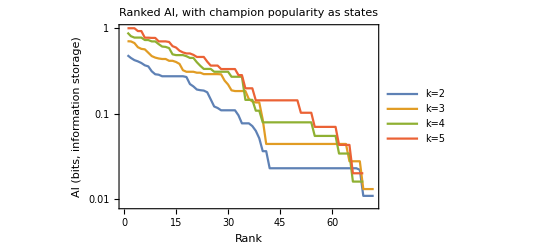

```mathematica
popplot=ListLogPlot[Reverse/@Sort/@pai,Joined->True,PlotRange->All,PlotLabel->"Ranked AI, with champion popularity as states",Frame->True,FrameLabel->{"Rank","AI (bits, information storage)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
totpai = Table[

Table[

acttotal=Partition[pop[[j]],k+1,1];
actpast=Partition[pop[[j]],k,1];
actfuture=Partition[pop[[j]],1,1];

Table[

pxnk=Count[acttotal,acttotal[[i]]]/Length[acttotal];
pxk=Count[actpast,acttotal[[i]][[1;;k]]]/Length[actpast];
pxn=Count[actfuture,acttotal[[i]][[k+1;;k+1]]]/Length[actfuture];

Log[2,pxnk/(pxk*pxn)]//N

,{i,1,Length[acttotal]}]//Total
,{j,1,Length[pop]}]//Total

,{k,2,5}]
```

{133.604,207.147,267.76,296.399}

```mathematica
Export["population_AI_prelim.pdf",popplot]
```

population_AI_prelim.pdf

#### Winrate AI (need to explore thresholds), overall winrate

```mathematica
winsovertime=Table[
Table[

data={daysofdata[[k]][[l]]};
f[x_]:={x[[1]],x[[2]]/Length[data]};

names=f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally);
truefalse=Table[StringReplace[StringReplace[StringSplit[data[[i]][[13]],", "],"["->""],"]"->""],{i,1,Length[data]}]//ToExpression//Flatten;
wins=Table[If[(truefalse[[n]]//ToExpression)===True,names[[n]],{names[[n]][[1]],-1}],{n,1,Length[names]}];

series=Last/@Table[
If[MemberQ[Flatten[wins],champions[[j]]],wins[[Position[wins,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{l,1,Length[daysofdata[[k]]]}]//Mean
,{k,1,Length[daysofdata]}]//Transpose;
```

Make arbitrary threshold for more than 0 = 1 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]>0,1,0],{i,1,Length[x]}]
win=f/@winsovertime;
```

Do for k = 2 to 5

```mathematica
wai = Table[

Table[

acttotal1=Partition[win[[j]],k+1,1]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;
	actfuture1=Last/@acttotal1;

acttotal=Partition[win[[j]],k+1,1](*All possible chunks*);
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;
	actfuture=Last/@acttotal;

Table[pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
pxn=Count[actfuture,actfuture1[[i]]]/Length[actfuture];
pxnk*Log[2,pxnk/(pxk*pxn)]//N,{i,1,Length[acttotal1]}]//Total

,{j,1,Length[win]}]

,{k,2,5}];
```

```mathematica
a=Max/@wai
Table[
champions[[Flatten[Position[wai[[i]],a[[i]]]]//First]]
,{i,1,Length[a]}]
```

{0.420448,0.513398,0.970951,0.991076}

{JarvanIV,Ahri,Ahri,Blitzcrank}

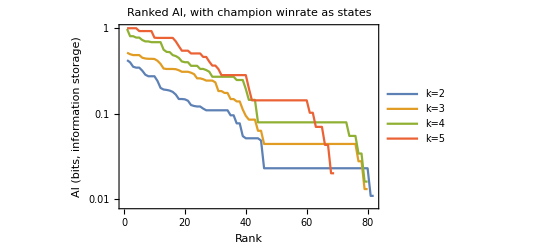

```mathematica
winplot=ListLogPlot[Reverse/@Sort/@wai,Joined->True,PlotRange->All,PlotLabel->"Ranked AI, with champion winrate as states",Frame->True,FrameLabel->{"Rank","AI (bits, information storage)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
totwai = Table[

Table[

acttotal=Partition[win[[j]],k+1,1];
actpast=Partition[win[[j]],k,1];
actfuture=Partition[win[[j]],1,1];

Table[

pxnk=Count[acttotal,acttotal[[i]]]/Length[acttotal];
pxk=Count[actpast,acttotal[[i]][[1;;k]]]/Length[actpast];
pxn=Count[actfuture,acttotal[[i]][[k+1;;k+1]]]/Length[actfuture];

Log[2,pxnk/(pxk*pxn)]//N

,{i,1,Length[acttotal]}]//Total
,{j,1,Length[win]}]//Total

,{k,2,5}]
```

{120.681,187.999,268.982,324.459}

```mathematica
Export["winrate_AI_prelim.pdf",winplot]
```

winrate_AI_prelim.pdf

#### Popularity TE

```mathematica
popularityovertime=

Table[
data=daysofdata[[k]];
f[x_]:={x[[1]],x[[2]]/Length[data]};

popularity=SortBy[f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally),First];

series=Last/@Table[
If[MemberQ[Flatten[popularity],champions[[j]]],popularity[[Position[popularity,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]≥(1/3),1,0],{i,1,Length[x]}]
pop=f/@popularityovertime;
```

Do k 2 through 5, all possible edges (not double-counted)

```mathematica
pte=Table[
Table[

ystates=Drop[pop,{j}];
xstate=pop[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]
,{j,1,Length[pop]-1}]//Flatten
,{k,2,5}];
```

```mathematica
pte[[1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,16507,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
 |  |  |  |

```mathematica
a=Max/@pte
i=1
Flatten[Position[pte[[i]],a[[i]]]]//First
Table[
champions[[Flatten[Position[pte[[i]],a[[i]]]]//First]]
,{i,1,Length[a]}]
```

{0.634137,0.558337,0.468996,0.503258}

1

15911

Part::partw: Part 15911 of {"Aatrox", "Ahri", "Akali", "Alistar", "Amumu", "Anivia", "Annie", "Ashe", "AurelionSol", "Azir", "Bard", "Blitzcrank", "Brand", "Braum", "Caitlyn", "Cassiopeia", "ChoGath", "Corki", "Darius", "Diana", "Draven", "Dr.Mundo", "Ekko", "Elise", "Evelynn", "Ezreal", "Fiddlesticks", "Fiora", "Fizz", "Galio", "Gangplank", "Garen", "Gnar", "Gragas", "Graves", "Hecarim", "Heimerdinger", "Illaoi", "Irelia", "Janna", "JarvanIV", "Jax", "Jayce", "Jhin", "Jinx", "Kalista", "Karma", "Karthus", "Kassadin", "Katarina", « 80 »} does not exist.

Part::partw: Part 8245 of {"Aatrox", "Ahri", "Akali", "Alistar", "Amumu", "Anivia", "Annie", "Ashe", "AurelionSol", "Azir", "Bard", "Blitzcrank", "Brand", "Braum", "Caitlyn", "Cassiopeia", "ChoGath", "Corki", "Darius", "Diana", "Draven", "Dr.Mundo", "Ekko", "Elise", "Evelynn", "Ezreal", "Fiddlesticks", "Fiora", "Fizz", "Galio", "Gangplank", "Garen", "Gnar", "Gragas", "Graves", "Hecarim", "Heimerdinger", "Illaoi", "Irelia", "Janna", "JarvanIV", "Jax", "Jayce", "Jhin", "Jinx", "Kalista", "Karma", "Karthus", "Kassadin", "Katarina", « 80 »} does not exist.

Part::partw: Part 10113 of {"Aatrox", "Ahri", "Akali", "Alistar", "Amumu", "Anivia", "Annie", "Ashe", "AurelionSol", "Azir", "Bard", "Blitzcrank", "Brand", "Braum", "Caitlyn", "Cassiopeia", "ChoGath", "Corki", "Darius", "Diana", "Draven", "Dr.Mundo", "Ekko", "Elise", "Evelynn", "Ezreal", "Fiddlesticks", "Fiora", "Fizz", "Galio", "Gangplank", "Garen", "Gnar", "Gragas", "Graves", "Hecarim", "Heimerdinger", "Illaoi", "Irelia", "Janna", "JarvanIV", "Jax", "Jayce", "Jhin", "Jinx", "Kalista", "Karma", "Karthus", "Kassadin", "Katarina", « 80 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{{Aatrox,Ahri,Akali,Alistar,Amumu,Anivia,Annie,Ashe,AurelionSol,Azir,Bard,Blitzcrank,Brand,Braum,Caitlyn,Cassiopeia,ChoGath,Corki,Darius,Diana,Draven,Dr.Mundo,Ekko,Elise,Evelynn,Ezreal,Fiddlesticks,Fiora,Fizz,Galio,Gangplank,Garen,Gnar,Gragas,Graves,Hecarim,Heimerdinger,Illaoi,Irelia,Janna,JarvanIV,Jax,Jayce,Jhin,Jinx,Kalista,Karma,Karthus,Kassadin,Katarina,Kayle,Kennen,KhaZix,Kindred,KogMaw,LeBlanc,LeeSin,Leona,Lissandra,Lucian,Lulu,Lux,Malphite,Malzahar,Maokai,MasterYi,MissFortune,Mordekaiser,Morgana,Nami,Nasus,Nautilus,Nidalee,Nocturne,Nunu,Olaf,Orianna,Pantheon,Poppy,Quinn,Rammus,RekSai,Renekton,Rengar,Riven,Rumble,Ryze,Sejuani,Shaco,Shen,Shyvana,Singed,Sion,Sivir,Skarner,Sona,Soraka,Swain,Syndra,TahmKench,Talon,Taric,Teemo,Thresh,Tristana,Trundle,Tryndamere,TwistedFate,Twitch,Udyr,Urgot,Varus,Vayne,Veigar,VelKoz,Vi,Viktor,Vladimir,Volibear,Warwick,Wukong,Xerath,XinZhao,Yasuo,Yorick,Zac,Zed,Ziggs,Zilean,Zyra}⟦15911⟧,{Aatrox,Ahri,Akali,Alistar,Amumu,Anivia,Annie,Ashe,AurelionSol,Azir,Bard,Blitzcrank,Brand,Braum,Caitlyn,Cassiopeia,ChoGath,Corki,Darius,Diana,Draven,Dr.Mundo,Ekko,Elise,Evelynn,Ezreal,Fiddlesticks,Fiora,Fizz,Galio,Gangplank,Garen,Gnar,Gragas,Graves,Hecarim,Heimerdinger,Illaoi,Irelia,Janna,JarvanIV,Jax,Jayce,Jhin,Jinx,Kalista,Karma,Karthus,Kassadin,Katarina,Kayle,Kennen,KhaZix,Kindred,KogMaw,LeBlanc,LeeSin,Leona,Lissandra,Lucian,Lulu,Lux,Malphite,Malzahar,Maokai,MasterYi,MissFortune,Mordekaiser,Morgana,Nami,Nasus,Nautilus,Nidalee,Nocturne,Nunu,Olaf,Orianna,Pantheon,Poppy,Quinn,Rammus,RekSai,Renekton,Rengar,Riven,Rumble,Ryze,Sejuani,Shaco,Shen,Shyvana,Singed,Sion,Sivir,Skarner,Sona,Soraka,Swain,Syndra,TahmKench,Talon,Taric,Teemo,Thresh,Tristana,Trundle,Tryndamere,TwistedFate,Twitch,Udyr,Urgot,Varus,Vayne,Veigar,VelKoz,Vi,Viktor,Vladimir,Volibear,Warwick,Wukong,Xerath,XinZhao,Yasuo,Yorick,Zac,Zed,Ziggs,Zilean,Zyra}⟦8245⟧,{Aatrox,Ahri,Akali,Alistar,Amumu,Anivia,Annie,Ashe,AurelionSol,Azir,Bard,Blitzcrank,Brand,Braum,Caitlyn,Cassiopeia,ChoGath,Corki,Darius,Diana,Draven,Dr.Mundo,Ekko,Elise,Evelynn,Ezreal,Fiddlesticks,Fiora,Fizz,Galio,Gangplank,Garen,Gnar,Gragas,Graves,Hecarim,Heimerdinger,Illaoi,Irelia,Janna,JarvanIV,Jax,Jayce,Jhin,Jinx,Kalista,Karma,Karthus,Kassadin,Katarina,Kayle,Kennen,KhaZix,Kindred,KogMaw,LeBlanc,LeeSin,Leona,Lissandra,Lucian,Lulu,Lux,Malphite,Malzahar,Maokai,MasterYi,MissFortune,Mordekaiser,Morgana,Nami,Nasus,Nautilus,Nidalee,Nocturne,Nunu,Olaf,Orianna,Pantheon,Poppy,Quinn,Rammus,RekSai,Renekton,Rengar,Riven,Rumble,Ryze,Sejuani,Shaco,Shen,Shyvana,Singed,Sion,Sivir,Skarner,Sona,Soraka,Swain,Syndra,TahmKench,Talon,Taric,Teemo,Thresh,Tristana,Trundle,Tryndamere,TwistedFate,Twitch,Udyr,Urgot,Varus,Vayne,Veigar,VelKoz,Vi,Viktor,Vladimir,Volibear,Warwick,Wukong,Xerath,XinZhao,Yasuo,Yorick,Zac,Zed,Ziggs,Zilean,Zyra}⟦10113⟧,{Aatrox,Ahri,Akali,Alistar,Amumu,Anivia,Annie,Ashe,AurelionSol,Azir,Bard,Blitzcrank,Brand,Braum,Caitlyn,Cassiopeia,ChoGath,Corki,Darius,Diana,Draven,Dr.Mundo,Ekko,Elise,Evelynn,Ezreal,Fiddlesticks,Fiora,Fizz,Galio,Gangplank,Garen,Gnar,Gragas,Graves,Hecarim,Heimerdinger,Illaoi,Irelia,Janna,JarvanIV,Jax,Jayce,Jhin,Jinx,Kalista,Karma,Karthus,Kassadin,Katarina,Kayle,Kennen,KhaZix,Kindred,KogMaw,LeBlanc,LeeSin,Leona,Lissandra,Lucian,Lulu,Lux,Malphite,Malzahar,Maokai,MasterYi,MissFortune,Mordekaiser,Morgana,Nami,Nasus,Nautilus,Nidalee,Nocturne,Nunu,Olaf,Orianna,Pantheon,Poppy,Quinn,Rammus,RekSai,Renekton,Rengar,Riven,Rumble,Ryze,Sejuani,Shaco,Shen,Shyvana,Singed,Sion,Sivir,Skarner,Sona,Soraka,Swain,Syndra,TahmKench,Talon,Taric,Teemo,Thresh,Tristana,Trundle,Tryndamere,TwistedFate,Twitch,Udyr,Urgot,Varus,Vayne,Veigar,VelKoz,Vi,Viktor,Vladimir,Volibear,Warwick,Wukong,Xerath,XinZhao,Yasuo,Yorick,Zac,Zed,Ziggs,Zilean,Zyra}⟦10079⟧}

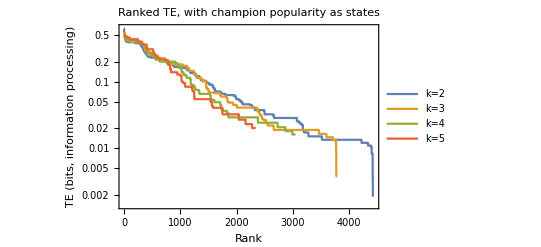

```mathematica
popplot=ListLogPlot[Reverse/@Sort/@pte,PlotRange->All,Joined->True,PlotLabel->"Ranked TE, with champion popularity as states",Frame->True,FrameLabel->{"Rank","TE (bits, information processing)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
Export["popularity_TE_prelim.pdf",popplot]
```

popularity_TE_prelim.pdf

#### Winrate TE

```mathematica
winsovertime=Table[
Table[

data={daysofdata[[k]][[l]]};
f[x_]:={x[[1]],x[[2]]/Length[data]};

names=f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally);
truefalse=Table[StringReplace[StringReplace[StringSplit[data[[i]][[13]],", "],"["->""],"]"->""],{i,1,Length[data]}]//ToExpression//Flatten;
wins=Table[If[(truefalse[[n]]//ToExpression)===True,names[[n]],{names[[n]][[1]],-1}],{n,1,Length[names]}];

series=Last/@Table[
If[MemberQ[Flatten[wins],champions[[j]]],wins[[Position[wins,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{l,1,Length[daysofdata[[k]]]}]//Mean
,{k,1,Length[daysofdata]}]//Transpose;
```

Make arbitrary threshold for more than 0 = 1 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]>0,1,0],{i,1,Length[x]}]
win=f/@winsovertime;
```

Do for k = 2 to 5

```mathematica
wte=Table[
Table[

ystates=Drop[win,{j}];
xstate=win[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]
,{j,1,Length[win]-1}]//Flatten
,{k,2,5}];
```

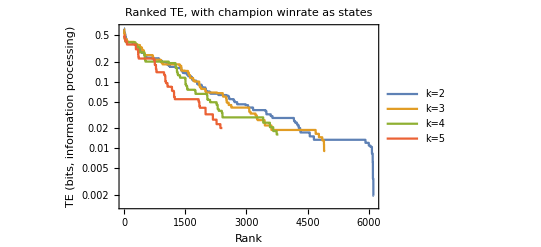

```mathematica
winplot=ListLogPlot[Reverse/@Sort/@wte,Joined->True,PlotRange->All,PlotLabel->"Ranked TE, with champion winrate as states",Frame->True,FrameLabel->{"Rank","TE (bits, information processing)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
Export["winrate_TE_prelim.pdf",winplot]
```

winrate_TE_prelim.pdf

#### Make graph of what champion beats who (micro wins, not overall winrate) (doesn’t include champions that were not played)

```mathematica
championgraphs=
Table[
graph=Table[

data=daysofdata[[k]][[l]];
f[x_]:={x[[4]],{x[[2]],x[[3]]},x[[1]],x[[5]]};

compare=GatherBy[f/@({StringSplit[StringReplace[data[[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]//Flatten,

StringSplit[StringReplace[data[[10]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]//Flatten,

StringSplit[StringReplace[data[[11]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]//Flatten,

StringSplit[StringReplace[data[[8]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]//Flatten,

StringSplit[StringReplace[data[[12]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]//Flatten//ToExpression
}//Transpose),First];

g[x_]:=Last/@x;
compare2=Sort/@compare//Transpose;
golds=g/@compare2;

Table[
If[(golds)[[i]][[1]]>(golds)[[i]][[2]],{compare2[[i]][[1]][[3]]->compare2[[i]][[2]][[3]]},{compare2[[i]][[2]][[3]]->compare2[[i]][[1]][[3]]}]
,{i,1,Length[compare2]}]

,{l,1,daysofdata[[k]]//Length}]//Flatten//DeleteDuplicates


(*
lonelynodes=DeleteCases[Table[If[MemberQ[Graph[graph]//VertexList,champions[[i]]]==False,{champions[[i]]->champions[[i]]}],{i,1,Length[champions]}],Null];

{graph,lonelynodes}//Flatten
*)


,{k,1,Length[daysofdata]}];
```

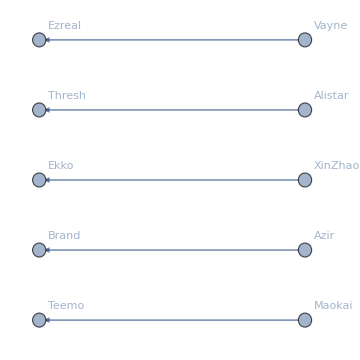
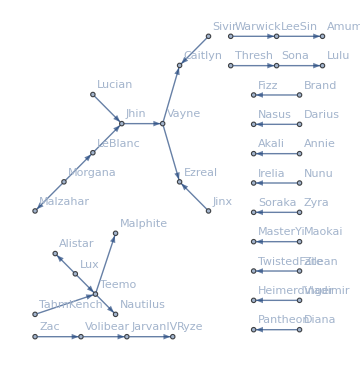
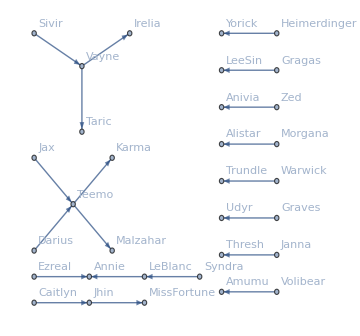
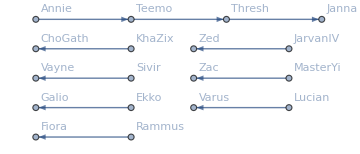
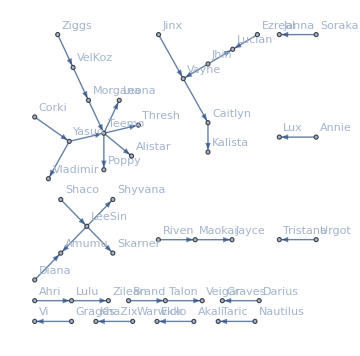
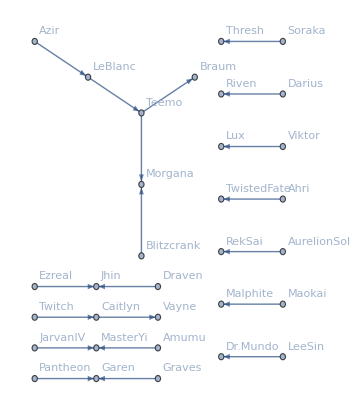
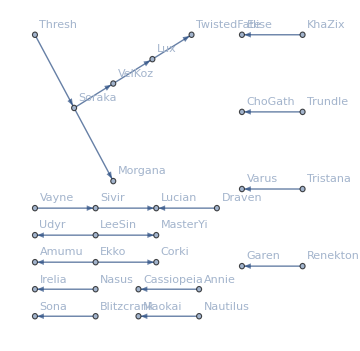
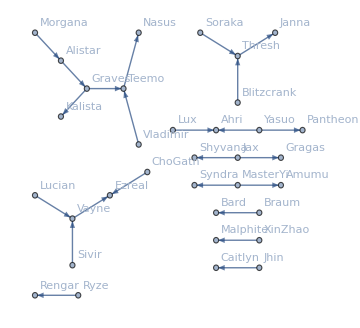

```mathematica
g[x_]:=Graph[x,VertexLabels->"Name",VertexSize->Medium,ImageSize->Medium,GraphLayout->"RadialEmbedding"]
g/@championgraphs
```

#### TE Between causal edges: Winrate

```mathematica
winsovertime=Table[
Table[

data={daysofdata[[k]][[l]]};
f[x_]:={x[[1]],x[[2]]/Length[data]};

names=f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally);
truefalse=Table[StringReplace[StringReplace[StringSplit[data[[i]][[13]],", "],"["->""],"]"->""],{i,1,Length[data]}]//ToExpression//Flatten;
wins=Table[If[(truefalse[[n]]//ToExpression)===True,names[[n]],{names[[n]][[1]],-1}],{n,1,Length[names]}];

series=Last/@Table[
If[MemberQ[Flatten[wins],champions[[j]]],wins[[Position[wins,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{l,1,Length[daysofdata[[k]]]}]//Mean
,{k,1,Length[daysofdata]}]//Transpose;
```

```mathematica
f[x_]:=Table[If[x[[i]]>0,1,0],{i,1,Length[x]}]
win=f/@winsovertime;
```

```mathematica
causalwte=
Table[
Table[

championlist=championgraphs[[l]]//Graph//VertexList;

Table[
(*do tables through championlist and championgraphs*)
champ=championlist[[j]];
champ2=Position[champions,champ]//Flatten;
causalchamps=DeleteCases[Graph[championgraphs[[l]][[First/@Position[championgraphs[[l]],champ]]]]//VertexList,champ];
causalchamps2=Table[Position[champions,causalchamps[[i]]],{i,1,Length[causalchamps]}]//Flatten;
xstate=win[[champ2]][[1]];
ystates=win[[causalchamps2]];

Table[(*Table through ystates*)
ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[(*Table through time*)
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N
,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]

,{j,1,Length[championlist]}]

,{l,1,Length[championgraphs]}]//Flatten

,{k,2,5}];
```

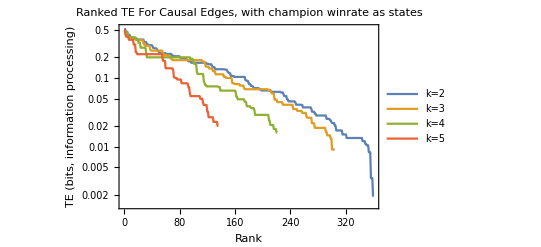

```mathematica
causalwinplot=ListLogPlot[Reverse/@Sort/@causalwte,Joined->True,PlotRange->All,PlotLabel->"Ranked TE For Causal Edges, with champion winrate as states",Frame->True,FrameLabel->{"Rank","TE (bits, information processing)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
Export["winrate_causalTE_prelim.pdf",causalwinplot]
```

winrate_causalTE_prelim.pdf

#### TE Between causal edges: Popularity

```mathematica
popularityovertime=

Table[
data=daysofdata[[k]];
f[x_]:={x[[1]],x[[2]]/Length[data]};

popularity=SortBy[f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally),First];

series=Last/@Table[
If[MemberQ[Flatten[popularity],champions[[j]]],popularity[[Position[popularity,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{k,1,Length[daysofdata]}]//Transpose;
```

```mathematica
f[x_]:=Table[If[x[[i]]≥(1/3),1,0],{i,1,Length[x]}]
pop=f/@popularityovertime;
```

```mathematica
causalpte=
Table[
Table[

championlist=championgraphs[[l]]//Graph//VertexList;

Table[
(*do tables through championlist and championgraphs*)
champ=championlist[[j]];
champ2=Position[champions,champ]//Flatten;
causalchamps=DeleteCases[Graph[championgraphs[[l]][[First/@Position[championgraphs[[l]],champ]]]]//VertexList,champ];
causalchamps2=Table[Position[champions,causalchamps[[i]]],{i,1,Length[causalchamps]}]//Flatten;
xstate=pop[[champ2]][[1]];
ystates=pop[[causalchamps2]];

Table[(*Table through ystates*)
ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[(*Table through time*)
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N
,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]

,{j,1,Length[championlist]}]

,{l,1,Length[championgraphs]}]//Flatten

,{k,2,5}];
```

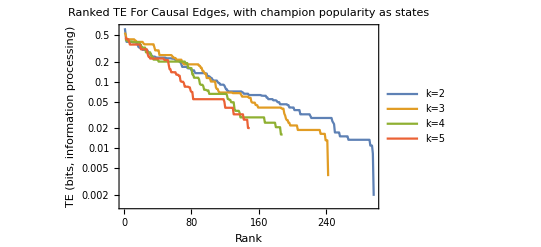

```mathematica
causalpopplot=ListLogPlot[Reverse/@Sort/@causalpte,Joined->True,PlotRange->All,PlotLabel->"Ranked TE For Causal Edges, with champion popularity as states",Frame->True,FrameLabel->{"Rank","TE (bits, information processing)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
Export["popularity_causalTE_prelim.pdf",causalpopplot]
```

popularity_causalTE_prelim.pdf

#### %Causal VS Popularity TE

```mathematica
popularityovertime=

Table[
data=daysofdata[[k]];
f[x_]:={x[[1]],x[[2]]/Length[data]};

popularity=SortBy[f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally),First];

series=Last/@Table[
If[MemberQ[Flatten[popularity],champions[[j]]],popularity[[Position[popularity,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]≥(1/3),1,0],{i,1,Length[x]}]
pop=f/@popularityovertime;

avgdegrees=Table[
Table[
If[VertexDegree[Graph[championgraphs[[i]]],champions[[j]]]//IntegerQ,
VertexDegree[Graph[championgraphs[[i]]],champions[[j]]],
0]
,{i,1,Length[championgraphs]}]//Mean
,{j,1,Length[champions]}];
```

Do k 2 through 5, all possible edges (not double-counted)

```mathematica
pte=Table[
Mean/@Table[

ystates=Drop[pop,{j}];
xstate=pop[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]
,{j,1,Length[pop]}]
,{k,2,5}];
```

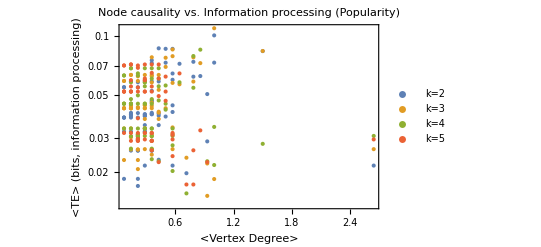

```mathematica
popplot=ListLogPlot[Table[Transpose[{avgdegrees,pte[[i]]}],{i,1,Length[pte]}],PlotRange->All,Joined->False,PlotLabel->"Node causality vs. Information processing (Popularity)",Frame->True,FrameLabel->{"<Vertex Degree>","<TE> (bits, information processing)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
Export["popularity_degvsTE_prelim.pdf",popplot]
```

popularity_degvsTE_prelim.pdf

#### %Causal VS Winrate TE

```mathematica
winsovertime=Table[
Table[

data={daysofdata[[k]][[l]]};
f[x_]:={x[[1]],x[[2]]/Length[data]};

names=f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally);
truefalse=Table[StringReplace[StringReplace[StringSplit[data[[i]][[13]],", "],"["->""],"]"->""],{i,1,Length[data]}]//ToExpression//Flatten;
wins=Table[If[(truefalse[[n]]//ToExpression)===True,names[[n]],{names[[n]][[1]],-1}],{n,1,Length[names]}];

series=Last/@Table[
If[MemberQ[Flatten[wins],champions[[j]]],wins[[Position[wins,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{l,1,Length[daysofdata[[k]]]}]//Mean
,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]>0,1,0],{i,1,Length[x]}]
win=f/@winsovertime;

avgdegrees=Table[
Table[
If[VertexDegree[Graph[championgraphs[[i]]],champions[[j]]]//IntegerQ,
VertexDegree[Graph[championgraphs[[i]]],champions[[j]]],
0]
,{i,1,Length[championgraphs]}]//Mean
,{j,1,Length[champions]}];
```

Do k 2 through 5, all possible edges (not double-counted)

```mathematica
wte=Table[
Mean/@Table[

ystates=Drop[win,{j}];
xstate=win[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]
,{j,1,Length[win]}]
,{k,2,5}];
```

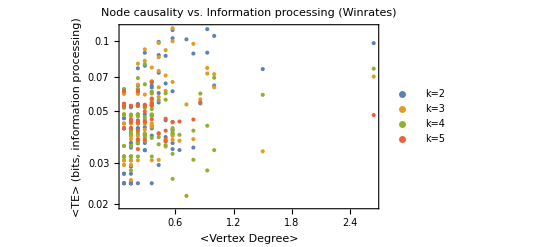

```mathematica
winplot=ListLogPlot[Table[Transpose[{avgdegrees,wte[[i]]}],{i,1,Length[wte]}],PlotRange->All,Joined->False,PlotLabel->"Node causality vs. Information processing (Winrates)",Frame->True,FrameLabel->{"<Vertex Degree>","<TE> (bits, information processing)"},PlotLegends->{"k=2","k=3","k=4","k=5"}]
```

```mathematica
Export["winrate_degvsTE_prelim.pdf",winplot]
```

winrate_degvsTE_prelim.pdf

#### Total TE per K: Popularity

```mathematica
popularityovertime=

Table[
data=daysofdata[[k]];
f[x_]:={x[[1]],x[[2]]/Length[data]};

popularity=SortBy[f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally),First];

series=Last/@Table[
If[MemberQ[Flatten[popularity],champions[[j]]],popularity[[Position[popularity,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]≥(1/3),1,0],{i,1,Length[x]}]
pop=f/@popularityovertime;
```

Do k 2 through 5, all possible edges (not double-counted)

```mathematica
pte=Table[
Table[

ystates=Drop[pop,{j}];
xstate=pop[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]//Total
,{j,1,Length[pop]}]//Total
,{k,2,5}];
```

```mathematica
Transpose[{Range[2,5],pte}]
```

{431.617,425.828,381.889,360.084}

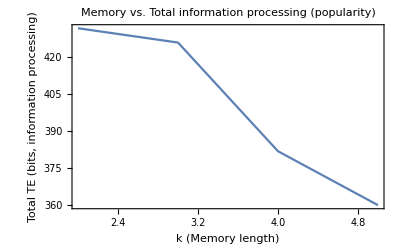

```mathematica
popplot=ListLinePlot[Transpose[{Range[2,5],pte}],PlotRange->All,PlotLabel->"Memory vs. Total information processing (popularity)",Frame->True,FrameLabel->{"k (Memory length)","Total TE (bits, information processing)"}]
```

```mathematica
Export["popularity_memvsTE_prelim.pdf",popplot]
```

popularity_memvsTE_prelim.pdf

#### Total TE per K: Winrate

```mathematica
winsovertime=Table[
Table[

data={daysofdata[[k]][[l]]};
f[x_]:={x[[1]],x[[2]]/Length[data]};

names=f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally);
truefalse=Table[StringReplace[StringReplace[StringSplit[data[[i]][[13]],", "],"["->""],"]"->""],{i,1,Length[data]}]//ToExpression//Flatten;
wins=Table[If[(truefalse[[n]]//ToExpression)===True,names[[n]],{names[[n]][[1]],-1}],{n,1,Length[names]}];

series=Last/@Table[
If[MemberQ[Flatten[wins],champions[[j]]],wins[[Position[wins,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{l,1,Length[daysofdata[[k]]]}]//Mean
,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]>0,1,0],{i,1,Length[x]}]
win=f/@winsovertime;
```

Do k 2 through 5, all possible edges (not double-counted)

```mathematica
wte=Table[
Table[

ystates=Drop[win,{j}];
xstate=win[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total

,{m,1,Length[ystates]}]//Total
,{j,1,Length[win]}]//Total
,{k,2,5}];
```

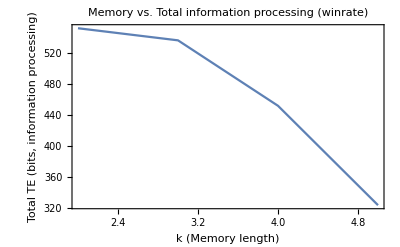

```mathematica
popplot=ListLinePlot[Transpose[{Range[2,5],wte}],PlotRange->All,PlotLabel->"Memory vs. Total information processing (winrate)",Frame->True,FrameLabel->{"k (Memory length)","Total TE (bits, information processing)"}]
```

```mathematica
Export["winrate_memvsTE_prelim.pdf",popplot]
```

winrate_memvsTE_prelim.pdf

#### AI vs AI vs TE Heatmap: Popularity

```mathematica
popularityovertime=

Table[
data=daysofdata[[k]];
f[x_]:={x[[1]],x[[2]]/Length[data]};

popularity=SortBy[f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally),First];

series=Last/@Table[
If[MemberQ[Flatten[popularity],champions[[j]]],popularity[[Position[popularity,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]≥(1/3),1,0],{i,1,Length[x]}]
pop=f/@popularityovertime;
```

Reorder pop so that lowest AI is first, and highest is last

```mathematica
pai = Table[

Table[

acttotal1=Partition[pop[[j]],k+1,1]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;
	actfuture1=Last/@acttotal1;

acttotal=Partition[pop[[j]],k+1,1](*All possible chunks*);
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;
	actfuture=Last/@acttotal;

Table[pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
pxn=Count[actfuture,actfuture1[[i]]]/Length[actfuture];
pxnk*Log[2,pxnk/(pxk*pxn)]//N,{i,1,Length[acttotal1]}]//Total

,{j,1,Length[pop]}]

,{k,2,5}];
```

```mathematica
order=Table[First/@SortBy[Transpose[{Range[1,130],pai[[i]]}],Last],{i,1,Length[pai]}];
pops=Table[pop[[order[[i]]]],{i,1,Length[order]}];
```

```mathematica
aiplots=Table[Last/@Table[SortBy[Transpose[{Range[1,130],pai[[i]]}],Last],{i,1,Length[pai]}][[j]],{j,1,Length[pops]}];
```

```mathematica
pte=Table[
pop=pops[[k-1]]; (*CAREFUL! K VALUES MAY CHANGE!*)
Table[

ystates=pop;
xstate=pop[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];
If[ystate==xstate,0,

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total
]
,{m,1,Length[ystates]}]//Reverse
,{j,1,Length[pop]}]
,{k,2,5}];
```

```mathematica
k=4;
heatmap=Column[{MatrixPlot[pte[[k]],PlotLabel->"TE (bits processed)",FrameLabel->{"AI(x) (bits stored)","AI(y) (bits stored)"},FrameTicks->None,PlotLegends->Automatic],ListLinePlot[aiplots[[k]],Axes->{False,True},Ticks->{None,{0,0.25,0.5,0.75,1}},AspectRatio->1/4]}];

Export["popularity_AI_vs_AI_vs_TE_Heatmap_k5.pdf",heatmap]
```

popularity_AI_vs_AI_vs_TE_Heatmap_k5.pdf

#### AI vs AI vs TE Heatmap: Winrate

```mathematica
winsovertime=Table[
Table[

data={daysofdata[[k]][[l]]};
f[x_]:={x[[1]],x[[2]]/Length[data]};

names=f/@(Table[
StringSplit[StringReplace[data[[i]][[9]],{"'"->"","\""->""," "->"","["->"","]"->""}],","]
,{i,1,Length[data]}]//Flatten//Tally);
truefalse=Table[StringReplace[StringReplace[StringSplit[data[[i]][[13]],", "],"["->""],"]"->""],{i,1,Length[data]}]//ToExpression//Flatten;
wins=Table[If[(truefalse[[n]]//ToExpression)===True,names[[n]],{names[[n]][[1]],-1}],{n,1,Length[names]}];

series=Last/@Table[
If[MemberQ[Flatten[wins],champions[[j]]],wins[[Position[wins,champions[[j]]][[1]][[1]]]],{champions[[j]],0}]
,{j,1,Length[champions]}]

,{l,1,Length[daysofdata[[k]]]}]//Mean
,{k,1,Length[daysofdata]}]//Transpose;
```

Much easier to write the time series for the individual champs
Make arbitrary threshold for 1/3 (to CG to 1’s and 0’s)

```mathematica
f[x_]:=Table[If[x[[i]]>0,1,0],{i,1,Length[x]}]
win=f/@winsovertime;
```

Reorder pop so that lowest AI is first, and highest is last

```mathematica
wai = Table[

Table[

acttotal1=Partition[win[[j]],k+1,1]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;
	actfuture1=Last/@acttotal1;

acttotal=Partition[win[[j]],k+1,1](*All possible chunks*);
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;
	actfuture=Last/@acttotal;

Table[pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
pxn=Count[actfuture,actfuture1[[i]]]/Length[actfuture];
pxnk*Log[2,pxnk/(pxk*pxn)]//N,{i,1,Length[acttotal1]}]//Total

,{j,1,Length[win]}]

,{k,2,5}];
```

```mathematica
order=Table[First/@SortBy[Transpose[{Range[1,130],wai[[i]]}],Last],{i,1,Length[wai]}];
wins=Table[win[[order[[i]]]],{i,1,Length[order]}];
```

```mathematica
aiplots=Table[Last/@Table[SortBy[Transpose[{Range[1,130],wai[[i]]}],Last],{i,1,Length[wai]}][[j]],{j,1,Length[wins]}];
```

```mathematica
wte=Table[
win=wins[[k-1]]; (*CAREFUL! K VALUES MAY CHANGE!*)
Table[

ystates=win;
xstate=win[[j]];

Table[

ystate=ystates[[m]];
ycolumn=ystate[[k;;-2]];
If[ystate==xstate,0,

xytotal1=Transpose[{ycolumn,Partition[xstate,k+1,1]}]//DeleteDuplicates (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast1=f/@xytotal1;
acttotal1=Last/@xytotal1;
f[x_]:=x[[1;;k]];
	actpast1=f/@acttotal1;

xytotal=Transpose[{ycolumn,Partition[xstate,k+1,1]}] (*All possible chunks,but delete the ones that are repeated*);
	f[x_]:={x[[1]],x[[2]][[1;;k]]};
	xypast=f/@xytotal;
acttotal=Last/@xytotal;
f[x_]:=x[[1;;k]];
	actpast=f/@acttotal;


(*the equation*)
Table[
pxnk=Count[acttotal,acttotal1[[i]]]/Length[acttotal];
pxk=Count[actpast,actpast1[[i]]]/Length[actpast];
denom=pxnk/pxk;

pxnky=Count[xytotal,xytotal1[[i]]]/Length[xytotal];
pxky=Count[xypast,xypast1[[i]]]/Length[xypast];
numerator=pxnky/pxky;

pxnky*Log[2,numerator/denom]//N,{i,1,Length[acttotal1]}]//Total
]
,{m,1,Length[ystates]}]//Reverse
,{j,1,Length[win]}]
,{k,2,5}];
```

```mathematica
k=4;
heatmap=Column[{MatrixPlot[wte[[k]],PlotLabel->"TE (bits processed)",FrameLabel->{"AI(x) (bits stored)","AI(y) (bits stored)"},FrameTicks->None,PlotLegends->Automatic],ListLinePlot[aiplots[[k]],PlotRange->All,Axes->{False,True},Ticks->{None,{0,0.25,0.5,0.75,1}},AspectRatio->1/4]}];

Export["winrate_AI_vs_AI_vs_TE_Heatmap_k5.pdf",heatmap]
```

winrate_AI_vs_AI_vs_TE_Heatmap_k5.pdf

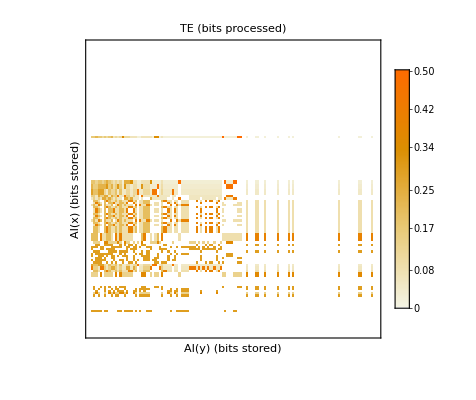
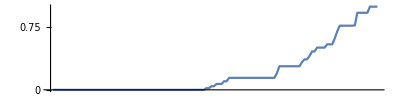

```mathematica
heatmap
```

#### The Entire network

```mathematica
graph=Graph[championgraphs//Flatten];
HighlighVertexDegree[g_,vd_]:=HighlightGraph[g,Table[Style[VertexList[g][[i]],ColorData["TemperatureMap"][vd[[i]]/Max[vd]]],{i,VertexCount[g]}]];
vd=VertexOutDegree[graph];
HighlighVertexDegree[graph,vd]
```

-Graphics-